```mathematica
(* paper uses whicheta=1,whichrel=1,whichQs=2,keepsimple=1,whichpairs=2,whichtauterm=0,whichmode=1, for rtrans *)
(* paper uses whicheta=1,whichrel=1,whichQs=2,keepsimple=1,whichpairs=1,whichtauterm=0,whichmode=1 or 0, for rest of simplified results *)
```

```mathematica
(* 0 = all  1= rad only 2 = spitzer only *)
whicheta=1;

(* 0 = general 1 = nonrel 2 = rel *)
whichrel=1; 

(*  1 = RL Qs  2 = my paper Qs *)
whichQs=2;

(* 0 = no other approximations   1 = make normal approximations or notation cleanings *)
keepsimple=1;

(* 0 = full e + pairs   1 = pairs   2 = e only *)
whichpairs=1;

(* for whichpairs==2, need to choose 0 = both   1 = 2*Sqrt[3] or  2 = 3*tauradsca term *)
whichtauterm=0;

(* 0 = l modes  1 = m modes *)
whichmode=0;
```

```mathematica
(* Tune theconsts's r-> for each case so normalized correctly.
Use myr's result  *)
(* also tune npairs-> *)

If[whichmode==0,
(* check gamma*thetajet//.theconstsfull//.physicalconsts  !! *)
mylmode=15.28;
mymmode=0;
myradius=1*^14;
mynpairsovernefactor=6;
];
If[whichmode==1,
myradius=3*10^(13);
mylmode=1;
mymmode=1/10;
mynpairsovernefactor=6;
];

simpleconsts={mygamma0->1.15,myomegaffp->0.25*c/rfp}
physicalconsts={msun->1.989*10^(33),G->6.672*10^(-8) ,c->2.99792458*10^(10) ,avo->6.0221367*10^(23),q->4.8029*10^(-10),kb->1.380658*10^(-16),ergPmev->1.60217649*10^(-6),h->4.13566733*10^(-15)*10^(-6)*ergPmev,hbar->h/(2*Pi),amu->1/avo,mb->amu,me->9.10938215*10^(-31)*1000,sigmat->(8*Pi/3)*(q^4/(me^2*c^4)),re->q^2/(me*c^2),arad->Pi^2*kb^4/(15*(hbar*c)^3)}
(* thetajet->0.02 *)
theconstsnornopairs={BrfpG->3.2*10^(15),lmode->mylmode,mmode->mymmode,rfp->rl,rl->3*msun*G/c^2,zeta->10^4,gamma->700,nu->3/4,rmono->3*10^(10),thfp->Pi/2,omegaffp->myomegaffp,gamma0->mygamma0,Lptilde->1,Numlayers->1}//.simpleconsts;
theconsts=Join[theconstsnornopairs,{r->myradius}];
npairsconsts={npairs->mynpairsovernefactor*ne};
theconstsnonpairs=Join[theconsts,{Lptilde->1,Numlayers->1}];
theconstsfull=Join[theconsts,npairsconsts];
theconstsfullnornopairs=theconstsnornopairs;
(thetajet*gamma)//.theconsts//.physicalconsts(* Check what traceback along mono trajectory gives *)
footconsts={BrfpG->3.2*10^(15),rfp->rl,rl->3*msun*G/c^2,zeta->10^4,gamma->gamma0,r->rfp,rp->r,nu->3/4,rmono->3*10^(10),omegaffp->0.25*c/rfp,thfp->Pi/2,gamma0->1.15,lmode->2,mmode->0}
Sqrt[8*Pi*(zeta*rhob*c^2)//.footconsts//.physicalconsts]
Sqrt[8*Pi*(zeta*rhofp*c^2)//.footconsts//.physicalconsts]
```

{mygamma0→1.15,myomegaffp→(0.25 c)/rfp}

{msun→1.989×10^33,G→6.672×10^-8,c→2.99792×10^10,avo→6.02214×10^23,q→4.8029×10^-10,kb→1.38066×10^-16,ergPmev→1.60218×10^-6,h→4.13567×10^-21 ergPmev,hbar→h/(2 π),amu→1/avo,mb→amu,me→9.10938×10^-28,sigmat→(8 π q^4)/(3 c^4 me^2),re→q^2/(c^2 me),arad→(kb^4 π^2)/(15 c^3 hbar^3)}

15.2785

{BrfpG→3.2×10^15,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→gamma0,r→rfp,rp→r,nu→3/4,rmono→30000000000,omegaffp→(0.25 c)/rfp,thfp→π/2,gamma0→1.15,lmode→2,mmode→0}

1.45702×10^17

3.2×10^15

```mathematica
(* setup standard parms *)
nu=3/4
rmono=3*10^(10)
omegaffp=0.25*c/rfp
thfp=Pi/2
gamma0=1.15
lmode=2
mmode=0
(* remove below clear to try specific parameters *)
Clear[nu,rmono,omegaffp,thfp,gamma0,lmode,mmode]
```

3/4

30000000000

(0.25 c)/rfp

π/2

1.15

2

0

```mathematica
(* JET STRUCTURE *)
(* Bphi~r^(-1) -> Bsq~r^(-2) -> bsq~r^(-4) *)
mu=zeta/2.3
vp0=c*Sqrt[1-1/gamma0^2]

(* already in mono regime *)
thetajet=(rmono/rfp)^(-nu/2)*(2*Sin[thfp/2])

Brcoll=BrfpG*(r/rfp)^(nu-2)
Br=(Brcoll//.{r->rmono})*(rmono/r)^(2)
Bphicoll=BrfpG*(-2*rfp*omegaffp/c)*(r/rfp)^(nu-1)*Tan[thetajet/2]
Bphicoll=BrfpG*(-2*rfp*omegaffp/c)*(r/rfp)^(nu-1)*(thetajet/2)
Bphi=(Bphicoll//.{r->rmono})*(rmono/r)^(1)
(*bsqcoll=mu*rhob*c^2*(r/rfp)^(nu-2)*)
(*bsq=(bsqcoll//.{r->rmono})*(rmono/r)^(2)*)
Print["bsq"];
bsq=Bphi^2/gamma^2


rhofp=BrfpG^2/(8*Pi)/c^2/zeta
nbfp=rhofp/mb
Ye=1/2
nefp=nbfp*Ye

(* previously neglected gamma*thetaj*)
(*ne=nefp*(rfp/r)^(2) (*/(gammathetajet/(Sin[Pi/2]*gamma0))*)*)
(*ne=nefp*(rfp/r)^(2) /(gamma*thetajet/(Sin[Pi/2]*gamma0))*)
ne=nefp*(Br/BrfpG)*(gamma0*vp0/(gamma*c))
nb=ne/Ye
rhob=nb*mb
(* Compare zeta and mu -- appear to agree well for thetafp=pi/2 *)

mufp=gamma0+(BrfpG^2/(4*Pi))*rfp^2*Sin[thfp]*2*Tan[thfp/2]*omegaffp^2/(rhofp*gamma0*vp0*c^3)
sigma=mufp/gamma-1

(* Magnetic pressure *)
pm=bsq/(8*Pi);
(* magnetic energy density is same as pressure *)
um=pm;
```

0.434783 zeta

c √(1-1/gamma0^2)

2 (rmono/rfp)^(-nu/2) Sin[thfp/2]

BrfpG (r/rfp)^(-2+nu)

(BrfpG rmono^2 (rmono/rfp)^(-2+nu))/r^2

-(2 BrfpG omegaffp (r/rfp)^(-1+nu) rfp Tan[(rmono/rfp)^(-nu/2) Sin[thfp/2]])/c

-(2 BrfpG omegaffp (r/rfp)^(-1+nu) rfp (rmono/rfp)^(-nu/2) Sin[thfp/2])/c

-(2 BrfpG omegaffp rfp rmono (rmono/rfp)^(-1+nu/2) Sin[thfp/2])/(c r)

bsq

(4 BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(c^2 gamma^2 r^2)

BrfpG^2/(8 c^2 π zeta)

BrfpG^2/(8 c^2 mb π zeta)

1/2

BrfpG^2/(16 c^2 mb π zeta)

(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)

(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(8 c^2 gamma mb π r^2 zeta)

(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(8 c^2 gamma π r^2 zeta)

gamma0+(4 omegaffp^2 rfp^2 zeta Sin[thfp] Tan[thfp/2])/(c^2 √(1-1/gamma0^2) gamma0)

-1+(gamma0+(4 omegaffp^2 rfp^2 zeta Sin[thfp] Tan[thfp/2])/(c^2 √(1-1/gamma0^2) gamma0))/gamma

```mathematica
(* JET SUBSTRUCTURE *)
Rjet=r*Sin[thetajet]
Rjet=r*thetajet;
If[keepsimple==1,
(* l modes choosing l=2 *)
If[whichmode==0,
(* must ensure mylmode≥gamma*thetajet *)
(*Lp=Lptilde*(Pi*Rjet)/(mylmode);*)
Lp=Lptilde*(Pi*Rjet)/(gamma*thetajet);
];
(* m modes  choosing m=0.1 *)
If[whichmode==1,
Lp=Lptilde*(gamma*2*Pi*c)/(mymmode*omegaffp);
];
];
If[keepsimple==0,
(* must ensure mylmode≥gamma*thetajet *)
(*Lp=1/(1/(Pi*Rjet/(mylmode))+mymmode*omegaffp/(gamma*2*Pi*c));*)
Lp=1/(1/(Pi*Rjet/(gamma*thetajet))+mymmode*omegaffp/(gamma*2*Pi*c));
];
```

r Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]

```mathematica
(* for testing synch power vs. simple power and per-particle energy vs. estimate *)
ne4[rhob_]:=(rhob/mb*Ye)//.physicalconsts;
netot4[rhob_,npairs_]:=ne4[rhob]+npairs;
Thetadep2[T_]:=(kb*T)/(me*c^2);
beta2[gamma_]:=Sqrt[1-1/gamma^2];
fgamfullfree2[T_]:=1/(Thetadep2[T]*BesselK[2,1/Thetadep2[T]]);
fgamfullfixedT2[gamma_,T_]:=gamma^2*beta2[gamma]*Exp[-gamma/Thetadep2[T]];
jclassgen2[gamma_,bgauss_]:=2*q^4*bgauss^2*(gamma^2-1)/(3*me^2*c^3);
pitchpart=Integrate[Sin[th]^3,{th,0,Pi}]; (* emissivity has Sin[thetap]^2 and then assume isotropic, so density weight is Sin[thetap]d\thetap *)
Pclassgen2[rhob_,T_,bgauss_,npairs_]:=Module[{omegap,gammap},netot4[rhob,npairs]*fgamfullfree2[T]*NIntegrate[pitchpart*fgamfullfixedT2[gammap,T]*jclassgen2[gammap,bgauss],{gammap,1,Infinity}]];

(*Fsyn[omegap_?NumericQ]:=omegap*NIntegrate[BesselK[5/3,x],{x,omegap,Infinity}];*)
Fsyn[x0_]:=x0*((2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},x0^2/4])/x0^(2/3)+(π (-320+(81 2^(1/3) x0^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},x0^2/4])/Gamma[-1/3]))/(320 √3));
omegacfun[gammap_?NumericQ,bgauss_?NumericQ]:=3*gammap^2*q*bgauss/(2*me*c)//.physicalconsts;
jclassgen3[omega_?NumericQ,gamma_?NumericQ,bgauss_?NumericQ]:=(Sqrt[3]/(2*Pi)*q^3*bgauss/(me*c^2)//.physicalconsts)*Fsyn[omega/omegacfun[gamma,bgauss]];
integrand[rhob_?NumericQ,gammap_?NumericQ,T_?NumericQ,npairs_?NumericQ,omega_?NumericQ,bgauss_?NumericQ]:=(netot4[rhob,npairs]//.theconsts//.physicalconsts)*fgamfullfree2[T]*pitchpart*fgamfullfixedT2[gammap,T]*jclassgen3[omega,gammap,bgauss];

Pofomega[rhob_?NumericQ,T_?NumericQ,bgauss_?NumericQ,npairs_?NumericQ,omega_?NumericQ]:=Module[{gammap},NIntegrate[integrand[rhob,gammap,T,npairs,omega,bgauss],{gammap,1,Infinity}]];

pmom[gam_]:=Sqrt[gam^2-1]*me*c//.physicalconsts
Eele[gam_]:=Sqrt[pmom[gam]^2*c^2+me^2*c^4]//.physicalconsts
Npart[rhob_,T_,bgauss_,npairs_]:=Module[{gammap},fgamfullfree2[T]*NIntegrate[pitchpart*fgamfullfixedT2[gammap,T],{gammap,1,Infinity}]];
Epart[rhob_,T_,bgauss_,npairs_]:=Module[{omegap,gammap},fgamfullfree2[T]*NIntegrate[Eele[gammap]*pitchpart*fgamfullfixedT2[gammap,T],{gammap,1,Infinity}]];
Eperparticle[rhob_,T_,bgauss_,npairs_]:=Epart[rhob,T,bgauss,npairs]/Npart[rhob,T,bgauss,npairs];
```

```mathematica
(* both pairs for etae=0 *)
Eefull[x_]:=Sqrt[x^2+(me*c^2)^2]//.physicalconsts;
Fefull[E_,T_]:=1/(Exp[E/(kb*T)]+1)//.physicalconsts;
ppairsfull[T_]:=(2/(3*Pi^2*(hbar*c)^3)//.physicalconsts)*NIntegrate[x^4/Eefull[x]*Fefull[Eefull[x],T],{x,0,Infinity}];
upairsfull[T_]:=(2/(Pi^2*(hbar*c)^3)//.physicalconsts)*NIntegrate[x^2*Eefull[x]*Fefull[Eefull[x],T],{x,0,Infinity}];
npairsfull[T_,rhob_]:=(2/(Pi^2*(hbar*c)^3)//.theconsts//.physicalconsts)*NIntegrate[x^2*Fefull[Eefull[x],T],{x,0,Infinity}]-(ne4[rhob]//.theconsts//.physicalconsts);
```

```mathematica
(* GAS PRESSURE *)
(*vrsp=eta/deltasp*)
(*vrdiss=vrsp*)
(*vrdiss=c*)
(*Qr=(2*bsq*vrdiss)//.{Lp->Rjet}*)

(* scat across entire jet, not just Lp *)
If[keepsimple==0,
Numm=Max[1,mmode];
Numm=mmode;
Numl=lmode-1;
Numlayers=Max[Numm,Numl];
Numlayers=1; (* was stupid to have this *)
]
If[keepsimple==1,
(* keep simple -- lmode represents Numlayers actually *)
Clear[Numlayers];
Numlayers=1; (* was stupid to have this *)
];
 
If[whichpairs==0,
tausca=sigmat*(ne*Rjet+npairs*Lp*Numlayers);
];
If[whichpairs==1,
tausca=sigmat*(npairs*Lp*Numlayers);
];
If[whichpairs==2,
tausca=sigmat*ne*Rjet;
];

(* abs *)
(* Synch emission energy density rate *)
(* 1/2 m c^2 (v/c) ^2 = (3/2) kb T *)
thetae=(kb*T)/(me*c^2)
Thetae=(3/2)*thetae
ve=c*Sqrt[Thetae*(2+Thetae)]/(1+Thetae)
venonrel=c*Sqrt[3*kb*T/(me*c^2)]
gammae=1/Sqrt[1-(ve/c)^2]
gammaultra=Sqrt[2]*Thetae

If[whichpairs==0,
netot=ne+npairs;
];
If[whichpairs==1,
netot=npairs;
];
If[whichpairs==2,
netot=ne;
];

(* as in RL -- no integral over pitch angles -- but averages to get per particle *)
Qs1=netot*(4/3)*sigmat*c*(gammae^2-1)*pm
(* APPROX rel *)
Qsrel1=netot*(4/3)*sigmat*c*(gammaultra^2)*pm
(* APPROX nonrel *)
Qsnonrel1=netot*(4/3)*sigmat*c*(venonrel/c)^2*pm

(* as in paper with delta function in distribution function *)
jsynch=2*q^4*bsq*(gammae^2-1)*Integrate[Sin[hh]^2,{hh,0,Pi}]/(3*me^2*c^3);
jsynchrel=2*q^4*bsq*(gammaultra^2)*Integrate[Sin[hh]^2,{hh,0,Pi}]/(3*me^2*c^3);
jsynchnonrel=2*q^4*bsq*(venonrel/c)^2*Integrate[Sin[hh]^2,{hh,0,Pi}]/(3*me^2*c^3);
Qs2=netot*jsynch
Qsrel2=netot*jsynchrel
Qsnonrel2=netot*jsynchnonrel

(* choose out of accurate versions *)
If[whichQs==2,
Qs=Qs2;
Qsnonrel=Qsnonrel2;
Qsrel=Qsrel2;
];
If[whichQs==1,
Qs=Qs1;
Qsnonrel=Qsnonrel1;
Qsrel=Qsrel1;
];

(* choose gen or nonrel or rel *)
If[whichrel==0,
(* do nothing *)
1;
];
If[whichrel==1,
Qs=Qsnonrel;
];
If[whichrel==2,
Qs=Qsrel;
];

(* compute absorption optical depth *)
urad0=arad*T^4
dtauabsds=Qs/(c*urad0)
If[whichpairs==0,
tauabs=dtauabsds/netot*(ne*Rjet+npairs*Lp*Numlayers);
];
If[whichpairs==1,
tauabs=dtauabsds/netot*(npairs*Lp*Numlayers);
];
If[whichpairs==2,
tauabs=dtauabsds/netot*(ne*Rjet);
];
Habs=tauabs/dtauabsds

(* total *)
tautot=tauabs+tausca
If[keepsimple==0,
htau=(1/3)/(tautot/2+1/Sqrt[3]+1/(3*tauabs));
gtau=(3*tautot+2*Sqrt[3])/(3*tautot+2*Sqrt[3]+2/tauabs);
];
If[keepsimple==1,
(* assume tauabs<<1 but tausca\sim 1 *)
htau=(1/3)/(1/(3*tauabs));
gtau=(3*tausca+2*Sqrt[3])/(2/tauabs);
];
(* whichtauterm==0 taken care of in above *)
If[keepsimple== 1 && whichpairs==2&&whichtauterm==1,
(* also assume tausca<1<2sqrt(3) *)
(* assume tauabs<<1 but tausca\sim 1 *)
htau=(1/3)/(1/(3*tauabs));
gtau=(2*Sqrt[3])/(2/tauabs);
];
If[keepsimple== 1 && whichpairs==2&&whichtauterm==2,
(* also assume tausca<1<2sqrt(3) *)
(* assume tauabs<<1 but tausca\sim 1 *)
htau=(1/3)/(1/(3*tauabs));
gtau=(3*tausca)/(2/tauabs);
];

Frad=c*urad0*htau
Qrad=Frad/Habs
urad=urad0*gtau
prad=(4/3-1)*urad
nrad=urad/(4*kb*T)

(* pairs *)
pairfactor=Exp[-me*c^2/(kb*T)]
(* pairs approx *)
If[whichrel==0,
pairfactorsimple=pairfactor;
];
If[whichrel==1,
(* can't simplify it in the non-rel regime! *)
pairfactorsimple=pairfactor;
];
If[whichrel==2,
pairfactorsimple=1;
];
upairs=(7/4)*urad*pairfactor
ppairs=(4/3-1)*upairs

(* true pair density runs between 0.02 and 0.3 after pairs matter at about lT=8.2 *)
up={{10.01,0.3006}};
down={{8.196,0.01981}};
slope=(up[[1,2]]-down[[1,2]])/(up[[1,1]]-down[[1,1]]);
fit=down[[1,2]] + slope*(Log[10,T]-down[[1,1]]);
(* fit reduces the effective numbers of pairs compared to naive estimate *)
(*npairsfunc=upairs/(kb*T)*fit;*)
(* ok, still inaccurate due to upairs.  Since npairs a free parameter, just leave it and use full calculation for test plot *)
gtautemp1[T_,npairs_]=Evaluate[(gtau//.theconstsnonpairs//.physicalconsts)];
gtautemp2[T_,npairs_]:=Evaluate[(gtau//.theconstsnonpairs//.physicalconsts)];
npairsfunc[T_?NumericQ,npairs_?NumericQ]:=Module[{myrhob},
myrhob=rhob//.theconsts//.physicalconsts;
npairsfull[T,myrhob]*gtautemp2[T,npairs]
];

(* baryons & electrons *)
pb=nb*kb*T
pe=Ye*pb
ub=pb/(5/3-1)
ue=pe/(5/3-1) (* should be 4/3 when kbT>me*c^2 *)
ueultrarel=pe/(4/3-1)

If[keepsimple==0,
ug=urad+upairs+ub+ue;
pg=prad+ppairs+pb+pe;
];
If[keepsimple==1,
(* also assume radition pressure dominates *)
ug=urad;
pg=(4/3-1)*ug;
];
```

(kb T)/(c^2 me)

(3 kb T)/(2 c^2 me)

(√(3/2) c √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(1+(3 kb T)/(2 c^2 me))

√3 c √((kb T)/(c^2 me))

1/(√(1-(3 kb T (2+(3 kb T)/(2 c^2 me)))/(2 c^2 me (1+(3 kb T)/(2 c^2 me))^2)))

(3 kb T)/(√2 c^2 me)

1/(3 c gamma^2 π r^2)2 BrfpG^2 npairs omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat (-1+1/(1-(3 kb T (2+(3 kb T)/(2 c^2 me)))/(2 c^2 me (1+(3 kb T)/(2 c^2 me))^2))) Sin[thfp/2]^2

(3 BrfpG^2 kb^2 npairs omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat T^2 Sin[thfp/2]^2)/(c^5 gamma^2 me^2 π r^2)

(2 BrfpG^2 kb npairs omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat T Sin[thfp/2]^2)/(c^3 gamma^2 me π r^2)

(4 BrfpG^2 npairs omegaffp^2 π q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) (-1+1/(1-(3 kb T (2+(3 kb T)/(2 c^2 me)))/(2 c^2 me (1+(3 kb T)/(2 c^2 me))^2))) Sin[thfp/2]^2)/(3 c^5 gamma^2 me^2 r^2)

(6 BrfpG^2 kb^2 npairs omegaffp^2 π q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) T^2 Sin[thfp/2]^2)/(c^9 gamma^2 me^4 r^2)

(4 BrfpG^2 kb npairs omegaffp^2 π q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) T Sin[thfp/2]^2)/(c^7 gamma^2 me^3 r^2)

arad T^4

(4 BrfpG^2 kb npairs omegaffp^2 π q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(arad c^8 gamma^2 me^3 r^2 T^3)

(Lptilde π r)/gamma

(Lptilde npairs π r sigmat)/gamma+(4 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(arad c^8 gamma^3 me^3 r T^3)

(4 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) T Sin[thfp/2]^2)/(c^7 gamma^3 me^3 r)

(4 BrfpG^2 kb npairs omegaffp^2 π q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) T Sin[thfp/2]^2)/(c^7 gamma^2 me^3 r^2)

1/(c^8 gamma^3 me^3 r)2 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) (2 √3+(3 Lptilde npairs π r sigmat)/gamma) T Sin[thfp/2]^2

1/(3 c^8 gamma^3 me^3 r)2 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) (2 √3+(3 Lptilde npairs π r sigmat)/gamma) T Sin[thfp/2]^2

1/(2 c^8 gamma^3 me^3 r)BrfpG^2 Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) (2 √3+(3 Lptilde npairs π r sigmat)/gamma) Sin[thfp/2]^2

ⅇ^(-(c^2 me)/(kb T))

1/(2 c^8 gamma^3 me^3 r)7 BrfpG^2 ⅇ^(-(c^2 me)/(kb T)) kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) (2 √3+(3 Lptilde npairs π r sigmat)/gamma) T Sin[thfp/2]^2

1/(6 c^8 gamma^3 me^3 r)7 BrfpG^2 ⅇ^(-(c^2 me)/(kb T)) kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) (2 √3+(3 Lptilde npairs π r sigmat)/gamma) T Sin[thfp/2]^2

(BrfpG^2 √(1-1/gamma0^2) gamma0 kb rmono^2 (rmono/rfp)^(-2+nu) T)/(8 c^2 gamma mb π r^2 zeta)

(BrfpG^2 √(1-1/gamma0^2) gamma0 kb rmono^2 (rmono/rfp)^(-2+nu) T)/(16 c^2 gamma mb π r^2 zeta)

(3 BrfpG^2 √(1-1/gamma0^2) gamma0 kb rmono^2 (rmono/rfp)^(-2+nu) T)/(16 c^2 gamma mb π r^2 zeta)

(3 BrfpG^2 √(1-1/gamma0^2) gamma0 kb rmono^2 (rmono/rfp)^(-2+nu) T)/(32 c^2 gamma mb π r^2 zeta)

(3 BrfpG^2 √(1-1/gamma0^2) gamma0 kb rmono^2 (rmono/rfp)^(-2+nu) T)/(16 c^2 gamma mb π r^2 zeta)

```mathematica
(* OPTICAL DEPTH TO OBSERVER *)
dtaupar=ne*sigmat/(2*gamma)
taupar=FullSimplify[Integrate[dtaupar,{r,rp,Infinity}],{rp>0}]//.{rp->r}
dtauperp=ne*sigmat*gamma*r*2*thetajet
taualongjet=tausca + taupar
```

(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu) sigmat)/(32 c^2 gamma^2 mb π r^2 zeta)

(BrfpG^2 √(1-1/gamma0^2) gamma0 rfp^2 (rmono/rfp)^nu sigmat)/(32 c^2 gamma^2 mb π r zeta)

(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) sigmat Sin[thfp/2])/(4 c^2 mb π r zeta)

(Lptilde npairs π r sigmat)/gamma+(BrfpG^2 √(1-1/gamma0^2) gamma0 rfp^2 (rmono/rfp)^nu sigmat)/(32 c^2 gamma^2 mb π r zeta)

```mathematica
(* COLLISIONLESS SCALE *)
omegapi=Sqrt[4*Pi*nb*q^2/mb]
di=c/omegapi
omegape=Sqrt[4*Pi*netot*q^2/me]
de=c/omegape
```

(√((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rmono^2 (rmono/rfp)^(-2+nu))/(c^2 gamma mb^2 r^2 zeta)))/(√2)

(√2 c)/(√((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rmono^2 (rmono/rfp)^(-2+nu))/(c^2 gamma mb^2 r^2 zeta)))

2 √π √((npairs q^2)/me)

c/(2 √π √((npairs q^2)/me))

```mathematica
(* COLLISIONAL RECONNECTION *)
(* Spitzer resistivity alone would predict fast only at ridiculously large radii *)
(* mass = me mb /( me+mb) ~ me *)
(* too complicated with below -- just check it *)(*vth=c*Sqrt[(3/2)*thetae*(2+thetae)]/(1+thetae)*)
vth=ve;

(* force choosable whichrel instead of having split case as did for pressure *)
If[whichrel==0,
gammae=1/Sqrt[1-(vth/c)^2];
pmome=gammae*me*vth;
Ee=Sqrt[pmome^2*c^2+me^2*c^4]-me*c^2;
];
If[whichrel==1,
(* maybe it's always Ee order k_b T ? *)
Ee=(3/2)*kb*T;
];
If[whichrel==2,
pmomeapprox=gammaultra*me*c;
Eeapprox=pmomeapprox*c;
];

lambdad=vth/omegape (* was inverted *)
lambdac=Sqrt[5/(16*Pi)]*q^2/Ee
logLtrue=Log[lambdad/lambdac]
logL=30; (* compare to actual logLtrue for typical radius and parameters *)
(*etas=(5*Sqrt[3]/(32*Pi))*c*re*(thetae)^(-3/2)*logL*)
sigma0=Pi*lambdac^2
sigmac=sigma0*logL
lambdamfp=1/(netot*sigmac)
nuc=vth/lambdamfp
(* rel spitzer *)
etas=de^2*nuc
(* Use photon drag term *)
nucg=(4/3)*(urad*sigmat*c)/(me*c^2)
etag=de^2*nucg
(* CHOOSE *)
eta=If[whicheta==1,eta=etag,If[whicheta==2,etas,etag+etas]];
```

(c √(3/(2 π)) √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(2 √((npairs q^2)/me) (1+(3 kb T)/(2 c^2 me)))

(√(5/π) q^2)/(6 kb T)

Log[(3 √(3/10) c kb T √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(q^2 √((npairs q^2)/me) (1+(3 kb T)/(2 c^2 me)))]

(5 q^4)/(36 kb^2 T^2)

(25 q^4)/(6 kb^2 T^2)

(6 kb^2 T^2)/(25 npairs q^4)

(25 c npairs q^4 √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(2 √6 kb^2 T^2 (1+(3 kb T)/(2 c^2 me)))

(25 c^3 me q^2 √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(8 √6 kb^2 π T^2 (1+(3 kb T)/(2 c^2 me)))

1/(3 c^9 gamma^3 me^4 r)8 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat (2 √3+(3 Lptilde npairs π r sigmat)/gamma) T Sin[thfp/2]^2

1/(3 c^7 gamma^3 me^3 r)2 BrfpG^2 kb Lptilde omegaffp^2 π q^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat (2 √3+(3 Lptilde npairs π r sigmat)/gamma) T Sin[thfp/2]^2

```mathematica
(* Check foot point values and traceback-mono value *)
rhob//.footconsts//.physicalconsts
rhofp//.footconsts//.physicalconsts
```

9.39829×10^7

45333.4

```mathematica
(* check that results in number with any T *)
pmnum=pm//.footconsts//.physicalconsts

pg//.{T->2*10^11,npairs->ne,Lptilde->1,Numlayers->1}//.footconsts//.physicalconsts
pg//.{T->3*10^13,npairs->ne,Lptilde->1,Numlayers->1}//.theconsts//.physicalconsts
```

1.61673×10^32

1.33288×10^61

7.93145×10^13

```mathematica
(* FIND TEMPERATURE FROM PRESSURE BALANCE and npairs balance *)
```

```mathematica
localconsts={T->10^lT,npairs->10^lnpairs,Lptilde->1,Numlayers->1};
pmtouse=pm//.theconsts//.physicalconsts;
pgtouse=pg//.localconsts//.theconsts//.physicalconsts;
netouse=ne//.localconsts//.theconsts//.physicalconsts;

If[whichpairs==0 || whichpairs==1,
(* full solution but numerical *)
Print["netouse=",netouse];
p1=ContourPlot[{pgtouse==pmtouse,npairsfunc[10^lT,10^lnpairs]==10^lnpairs},{lT,6,Log[10,5*10^9]},{lnpairs,Log[10,0.0001*netouse],Log[10,10000*netouse]}];
sols=FindRoot[{pgtouse==pmtouse,npairsfunc[10^lT,10^lnpairs]==10^lnpairs},{lT,8.5},{lnpairs,Log[10,5*10^(11)]},WorkingPrecision->40,MaxIterations->1000];
Print["sols=",sols];
1
];
If[whichpairs==2,
p1=Plot[{pgtouse,pmtouse},{lT,8.0,11}];
sols=FindRoot[{pgtouse==pmtouse},{lT,8.5},WorkingPrecision->40,MaxIterations->1000];
Print["sols=",sols];
];
```

netouse=9.12243×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.5956223093668314`*^-7}. NIntegrate obtained 2.7591771402639811718785563773282486304314022373018755825904943853×10^-2598 and 3.0290512623105054351699627025749702817307007573476645238502616566×10^-2600 for the integral and error estimates.

FindRoot::precw: The precision of the argument function ({3.384916312018308`*^-13 2^1 + lnpairs + lT 5^lnpairs + lT (2 √3 + 1.1193224848833843`*^-25 2^15 + lnpairs 5^12 + lnpairs) == 8.562060810255251`*^9, npairsfunc[10^lT, 10^lnpairs] == 10^lnpairs}) is less than WorkingPrecision (40.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.4890464281602789`*^-6}. NIntegrate obtained 6.70424×10^-29 and 3.28072×10^-33 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {lT, lnpairs} = {8.602785050661829197023184223462381960135`40., 12.63448896316043769229735116498163535647`40.}. Try perturbing the initial point(s).

sols={lT→8.602785050661829197023184223462381960135,lnpairs→12.63448896316043769229735116498163535647}

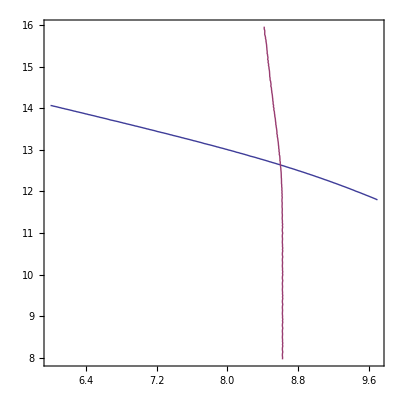

```mathematica
Show[{p1}]
```

```mathematica
10^10.7522203056579455594048864198488107274398473123255826067179`40./ne//.theconstsfull//.physicalconsts
```

0.0619598

```mathematica
10^13.3867647554380550164096534927457400004949082542374250159867`40./ne//.theconstsfull//.physicalconsts
```

26.7088

```mathematica
(*****************************************************)
(* from here on, assume npairs and Lp are parameters of model (not lmode or mmode directly) *)
(* this means use theconstsfull instead of theconsts to get numbers (not for finding solution though) *)
(*****************************************************)
```

```mathematica
eq=pg-pm==0;
solsTbraces=Solve[eq,T];
mysolsT=solsTbraces[[1]];
solsT=mysolsT;
```

```mathematica
testT=(mysolsT//.theconstsfull//.physicalconsts)[[1,2]]
Log[10,testT]
(* below big is good if nonrel approx used *)
(me*c^2/kb//.physicalconsts)/(testT)
```

2.7622×10^8

8.44125

21.4679

```mathematica
(* only 1 root now *)
myT=mysolsT[[1,2]];
```

```mathematica
(* check at relevant location *)
mysolsT//.theconstsfull//.physicalconsts
pm//.theconstsfull//.physicalconsts
pg//.mysolsT//.theconstsfull//.physicalconsts
```

{T→2.7622×10^8}

8.56206×10^9

8.56206×10^9

```mathematica
(* Check logL vs. logLtrue *)
logLtrue//.solsT//.theconstsfull//.physicalconsts
logL
```

24.8741

30

```mathematica
(* had below, that was incorrect -- giving ~100X speed of light *)
(*va=c*Sqrt[bsq/(rhob*c^2)]*)
(* below is correct, but gives too complicated an expression *)
(*va=c*Sqrt[bsq/(rhob*c^2+bsq)]*)
(* Below also correct, but doesn't give less complicated expession *)
(*va=c*Sqrt[1/(rhob*c^2/bsq+1)]*)
(* Just assume c, which is accurate, and gives simple expression *)
va=c;

(* UM10 *)
Qum0=bsq/(4*Pi*Lp/va);
(* don't include, just consider value later *)
Aum=Qrad/Qum0;

deltasp=Sqrt[Lp*eta/va];
deltapet=di;
conditionpt=deltapet/deltasp;
```

```mathematica
Aum//.solsT//.theconstsfull//.physicalconsts
deltasp//.solsT//.theconstsfull//.physicalconsts
deltapet//.solsT//.theconstsfull//.physicalconsts
conditionpt//.solsT//.theconstsfull//.physicalconsts
```

0.358622

25.3829

16.7984

0.661797

```mathematica
(* Check jet conditions *)
mysolsT//.theconstsfull//.physicalconsts
vth//.mysolsT//.theconstsfull//.physicalconsts
rhob//.theconstsfull//.physicalconsts
c^2*rhob//.theconstsfull//.physicalconsts
bsq//.theconstsfull//.physicalconsts
va//.theconstsfull//.physicalconsts
Print["Br"];
Br//.theconstsfull//.physicalconsts
Print["bsq/rho0c^2"]
(bsq/(8*Pi*rhob*c^2))//.theconstsfull//.physicalconsts
gamma//.theconstsfull//.physicalconsts
thetajet//.theconstsfull//.physicalconsts
gamma*thetajet//.theconstsfull//.physicalconsts
mufp//.theconstsfull//.physicalconsts
sigma//.theconstsfull//.physicalconsts
gtau//.mysolsT//.theconstsfull//.physicalconsts
Print["eta's"];
etas//.mysolsT//.theconstsfull//.physicalconsts
etag//.mysolsT//.theconstsfull//.physicalconsts
```

{T→2.7622×10^8}

1.06564×10^10

3.02963×10^-12

2.7229×10^9

2.15188×10^11

2.99792×10^10

Br

263.605

bsq/rho0c^2

3.14447

700

0.0218265

15.2785

4403.4

5.29058

5.83202×10^-10

eta's

0.458824

43.038

```mathematica
(* get rat with general Lp *)
rat=conditionpt//.solsT;
rat=FullSimplify[rat,{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0,gamma0>1,q>0,rmono>rfp,kb>0,omegaffp>0,sigmat>0,thfp>0,thfp≤Pi/2,npairs>0,lmode>0,mu>0,mu<2,gamma>1,c>0,me>0}];
solsrat=Solve[PowerExpand[rat]==1,r]
```

{{r→(((BrfpG^2 ((-1+gamma0) (1+gamma0))^(1/4) √Lptilde omegaffp rfp^(3-nu) rmono^nu √sigmat Sin[thfp/2])/(c^3 gamma^2 mb √npairs √zeta))^(2/3))/(2^(2/3) π^(1/3))}}

```mathematica
If[whichmode==0,
whichroot=1;
];
If[whichmode==1,
whichroot=2;
];
```

```mathematica
myr=FullSimplify[solsrat[[whichroot,1,2]],{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0,thfp>0,gamma>0,Lp>0}]
PowerExpand[myr]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
(* can use "theconsts" now since no r left *)
myrnum=myr//.theconstsfullnornopairs//.physicalconsts
myrnum=myr//.theconstsfull//.physicalconsts
```

(((BrfpG^2 (-1+gamma0^2)^(1/4) omegaffp rfp^(3-nu) rmono^nu √(Lptilde sigmat) Sin[thfp/2])/(c^3 gamma^2 mb √(npairs zeta)))^(2/3))/(2^(2/3) π^(1/3))

(BrfpG^(4/3) (-1+gamma0^2)^(1/6) Lptilde^(1/3) omegaffp^(2/3) rfp^((2 (3-nu))/3) rmono^(2 nu/3) sigmat^(1/3) Sin[thfp/2]^(2/3))/(2^(2/3) c^2 gamma^(4/3) mb^(2/3) npairs^(1/3) π^(1/3) zeta^(1/3))

(9.44804×10^-8 BrfpG^(4/3) Lptilde^(1/3) rfp^(-2/3+(2 (3-nu))/3) rmono^(2 nu/3) Sin[thfp/2]^(2/3))/(gamma^(4/3) npairs^(1/3) zeta^(1/3))

(2.32062×10^18)/npairs^(1/3)

1.31679×10^14

```mathematica
(* temperature *)
```

```mathematica
myT=FullSimplify[solsT[[1,2]]//.{r->myr},{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0,thfp>0,gamma>0,Lp>0}];
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
myTnum=myT//.theconstsfullnornopairs//.physicalconsts
myTnum=myT//.{zeta->gamma*13,gamma->x,npairs->y*ne}//.theconstsfull//.physicalconsts
```

(3.82464×10^40 gamma^(10/3) rfp^(-2/3 (2-nu)) rmono^(-2 nu/3) zeta^(1/3))/(BrfpG^(4/3) Lptilde^(4/3) npairs^(2/3) (4 √3 gamma+(1.18445×10^-30 BrfpG^(4/3) Lptilde^(4/3) npairs^(2/3) rfp^((2 (2-nu))/3) rmono^(2 nu/3) Sin[thfp/2]^(2/3))/(gamma^(4/3) zeta^(1/3))) Sin[thfp/2]^(2/3))

(7.63×10^20)/((2800 √3+0.0000290922 npairs^(2/3)) npairs^(2/3))

(0.0439206 x^13)/(y (x^11/(√(y/x^2)))^(2/3) (4 √3 x+(1.03142×10^12 y (1/(x^2 √(y/x)))^(2/3))/x^2))

```mathematica
(* tauabs=1 T *)
```

```mathematica
solsr=Solve[tauabs==1,r]
tauabs1r=solsr[[2,1,2]]
Ttaubs1=sols[[3,1,2]]//.{r->tauabs1r}
Ttaubs1=FullSimplify[Ttaubs1,{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0,thfp>0,gamma>0,Lp>0}];
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Ttaubs1num=Ttaubs1//.theconstsfullnornopairs//.physicalconsts
Ttaubs1num=Ttaubs1//.{zeta->gamma*13,gamma->x,npairs->y*ne}//.theconstsfull//.physicalconsts
```

{{r→(4 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^4 (rmono/rfp)^nu Sin[thfp/2]^2)/(arad c^8 gamma^3 me^3 T^3)}}

Part::partw: Part 2 of {{r → 4 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^4 (rmono/rfp)^nu Sin[thfp/2]^2/arad c^8 gamma^3 me^3 T^3}} does not exist.

{{r→(4 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^4 (rmono/rfp)^nu Sin[thfp/2]^2)/(arad c^8 gamma^3 me^3 T^3)}}⟦2,1,2⟧

Part::partw: Part 3 of {lT → 8.60278505066182919702318422346238196013451228439869455932864639180479571223259`40., lnpairs → 12.63448896316043769229735116498163535647312159804211972868870361708104610443115`40.} does not exist.

Part::partw: Part 2 of {{r → 4 BrfpG^2 kb Lptilde npairs omegaffp^2 π^2 q^4 rfp^4 (rmono/rfp)^nu Sin[thfp/2]^2/arad c^8 gamma^3 me^3 T^3}} does not exist.

{lT→8.602785050661829197023184223462381960135,lnpairs→12.63448896316043769229735116498163535647}⟦3,1,2⟧

{lT→8.602785050661829197023184223462381960135,lnpairs→12.63448896316043769229735116498163535647}⟦3,1,2⟧

{lT→8.602785050661829197023184223462381960135,lnpairs→12.63448896316043769229735116498163535647}⟦3,1,2⟧

«1 more identical outputs»

```mathematica
test=Log[10,myTnum//.{x->10^lx,y->10^ly}];
Plot3D[test,{lx,0,3},{ly,-1,1}]
```

-Graphics3D-

```mathematica
tauparexp=PowerExpand[taualongjet//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
tauparnum=taualongjet//.theconstsfull//.physicalconsts
tauparexp[[1]]//.theconstsfull//.physicalconsts
tauparexp[[2]]//.theconstsfull//.physicalconsts
```

(2.0894×10^-24 Lptilde npairs r)/gamma+(2.51737×10^-24 BrfpG^2 rfp^(2-nu) rmono^nu)/(gamma^2 r zeta)

1.67709

1.63375

0.0433366

```mathematica
tauparexpwithrtrans=PowerExpand[tauparexp//.{r->myr}//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
FullSimplify[tauparexpwithrtrans]
tauparexpwithrtransnum=tauparexpwithrtrans//.theconstsfull//.physicalconsts
```

(6.61169×10^-17 BrfpG^(2/3) npairs^(1/3) rfp^((2-nu)/3) rmono^(nu/3))/(gamma^(2/3) Lptilde^(1/3) zeta^(2/3) Sin[0.5 thfp]^(2/3))+(5.20634×10^-33 BrfpG^(4/3) Lptilde^(4/3) npairs^(2/3) rfp^((2 (2-nu))/3) rmono^(2 nu/3) Sin[0.5 thfp]^(2/3))/(gamma^(7/3) zeta^(1/3))

(6.61169×10^-17 BrfpG^(2/3) npairs^(1/3) rfp^(2/3-nu/3) rmono^(nu/3))/(gamma^(2/3) Lptilde^(1/3) zeta^(2/3) Sin[0.5 thfp]^(2/3))

0.723895

```mathematica
(* only use dominate term *)
taualongjetsimple=(sigmat*npairs*Lp*Numlayers);
tauparexp=PowerExpand[taualongjetsimple//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
tauparnum=taualongjetsimple//.{Lp->Pi*Rjet/(mylmode*gamma*thetajet),Numlayers->1}//.theconstsfull//.physicalconsts
```

(1.0447×10^-24 Lptilde npairs r)/gamma

0.0844373

```mathematica
(* plug in r -> rtrans *)
taualongjetsimpletrans=taualongjetsimple//.{r->myr}
tauparexptranstrans=PowerExpand[taualongjetsimpletrans//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
tauparnumtrans=taualongjetsimpletrans//.{Lp->Pi*Rjet/2,Numlayers->1}//.theconstsfull//.physicalconsts
```

(62.8319 c gamma Lptilde npairs sigmat)/omegaffp

1.67152×10^-22 gamma Lptilde npairs rfp

24.9613

```mathematica
(* look at other term *)
taualongjetsimple2=(2.5173658695220646*^-24 BrfpG^2 rfp^(2-nu) rmono^nu)/(gamma^2 r zeta)
tauparexp2=PowerExpand[taualongjetsimple2//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
tauparnum2=taualongjetsimple2//.{Lp->Pi*Rjet/2,Numlayers->1}//.theconstsfull//.physicalconsts
```

(2.51737×10^-24 BrfpG^2 rfp^(2-nu) rmono^nu)/(gamma^2 r zeta)

(2.51737×10^-24 BrfpG^2 rfp^(2-nu) rmono^nu)/(gamma^2 r zeta)

0.0866731

```mathematica
Tobs=((kb/ergPmev)*gamma)*PowerExpand[myT//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts];
Tobsexp=PowerExpand[Tobs//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Tobsexpnum=Tobsexp//.theconstsfull//.physicalconsts
Tobsexp1=(1.5569622956785853*^23 gamma rfp^-nu rmono^nu Csc[thfp/2])/(Lptilde npairs r (2 √3 rfp^(-nu/2) rmono^(nu/2)))
Tobsexp2=(1.5569622956785853*^23 gamma rfp^-nu rmono^nu Csc[thfp/2])/(Lptilde npairs r (6.2682059153469514*^-24 Lptilde npairs r Sin[thfp/2]))
(Tobsexp1)//.theconstsfull//.physicalconsts
(Tobsexp2)//.theconstsfull//.physicalconsts
```

(1.07164×10^-22 gamma)/((2.76118×10^-65 gamma^2 Lptilde^2 npairs^2+(1.90744×10^-43 gamma Lptilde npairs)/rfp) rfp^2)

29.2174

(4.49456×10^22 gamma rfp^(-nu/2) rmono^(nu/2) Csc[thfp/2])/(Lptilde npairs r)

(2.4839×10^46 gamma rfp^-nu rmono^nu Csc[thfp/2]^2)/(Lptilde^2 npairs^2 r^2)

2.63354

0.121827

```mathematica
700*(myT*kb/ergPmev//.theconstsfull//.physicalconsts)
```

29.2174

```mathematica
dttransitobs=Lp/(gamma*va)
dttransitobs=PowerExpand[dttransitobs//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts];
dttransitobsexp=PowerExpand[dttransitobs//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
dttransitobsexp//.theconstsfull//.physicalconsts
```

(Lptilde π r)/(c gamma^2)

(1.04792×10^-10 Lptilde r)/gamma^2

0.0213862

```mathematica
(* look at rdiss-rtrans *)
vrec=0.1*va
vrec=c
dtcodiss=Lp/(4*vrec)
rdissmrtrans=gamma*c*dtcodiss//.{r->myr}
rdissmrtrans=PowerExpand[rdissmrtrans//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
rdissmrtrans//.theconstsfull//.physicalconsts
```

0.1 c

c

(Lptilde π r)/(4 c gamma)

1/4 Lptilde (π/2)^(2/3) ((BrfpG^2 (-1+gamma0^2)^(1/4) omegaffp rfp^(3-nu) rmono^nu √(Lptilde sigmat) Sin[thfp/2])/(c^3 gamma^2 mb √(npairs zeta)))^(2/3)

(7.42048×10^-8 BrfpG^(4/3) Lptilde^(4/3) rfp^((2 (2-nu))/3) rmono^(2 nu/3) Sin[thfp/2]^(2/3))/(gamma^(4/3) npairs^(1/3) zeta^(1/3))

1.0342×10^14

```mathematica
Epeaksynobskevspruit=0.29*10^(-3)*1.7*10^(-8)*gamma*Sqrt[bsq]*gammae^2//.solsT//.theconstsfull//.physicalconsts
```

0.00403435

```mathematica
(* Spruit missed factor of 0.29 *)
```

```mathematica
pmuse=um
peuse=ueultrarel
fuck=FullSimplify[etaele*pmuse-peuse]
shit=Solve[fuck==0,zeta]
Tinj=(Solve[shit[[1,1,2]]==myzeta,T]//.{myzeta->zeta})[[1,1,2]]
gammaeinj=Simplify[gammae//.{T->Tinj}]
```

(BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(2 c^2 gamma^2 π r^2)

(3 BrfpG^2 √(1-1/gamma0^2) gamma0 kb rmono^2 (rmono/rfp)^(-2+nu) T)/(16 c^2 gamma mb π r^2 zeta)

-(BrfpG^2 rfp^2 (rmono/rfp)^nu (3 gamma √(1-1/gamma0^2) gamma0 kb T+4 etaele mb omegaffp^2 rfp^2 zeta (-1+Cos[thfp])))/(16 c^2 gamma^2 mb π r^2 zeta)

{{zeta→(3 gamma gamma0 √((-1+gamma0^2)/gamma0^2) kb T)/(4 (etaele mb omegaffp^2 rfp^2-etaele mb omegaffp^2 rfp^2 Cos[thfp]))}}

-(4 zeta (-etaele mb omegaffp^2 rfp^2+etaele mb omegaffp^2 rfp^2 Cos[thfp]))/(3 gamma gamma0 √((-1+gamma0^2)/gamma0^2) kb)

1/(√((c^4 gamma^2 (-1+gamma0^2) me^2)/((c^2 gamma √(1-1/gamma0^2) gamma0 me+2 etaele mb omegaffp^2 rfp^2 zeta-2 etaele mb omegaffp^2 rfp^2 zeta Cos[thfp])^2)))

```mathematica
gammajet=gamma;
```

```mathematica
Clear[gammaesyn,bsqsyn,gammajet]
Tobsconsts1={gammajet->gamma,gammaesyn->gammae,bsqsyn->bsq};
Tobsconsts2={gammajet->gamma,gammaesyn->gammaeinj,bsqsyn->bsq};
omegac=3*gammaesyn^2*q*Sqrt[bsqsyn]/(2*me*c)
omegapeak=0.29*omegac
Epeak=hbar*omegapeak
Print["Epeakobsmev"];
Epeakobsmev=gammajet*Epeak/ergPmev
Print["Epeakobskev"];
Epeakobskev=gammajet*Epeak/ergPmev*10^3
Epeakobskevthermal=Epeakobskev//.Tobsconsts1
Epeakobskevinj=Epeakobskev//.Tobsconsts2
```

(3 √bsqsyn gammaesyn^2 q)/(2 c me)

(0.435 √bsqsyn gammaesyn^2 q)/(c me)

(0.435 √bsqsyn gammaesyn^2 hbar q)/(c me)

Epeakobsmev

(0.435 √bsqsyn gammaesyn^2 gammajet hbar q)/(c ergPmev me)

Epeakobskev

(435. √bsqsyn gammaesyn^2 gammajet hbar q)/(c ergPmev me)

(870. gamma hbar q √((BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(c^2 gamma^2 r^2)))/(c ergPmev me (1-(3 kb T (2+(3 kb T)/(2 c^2 me)))/(2 c^2 me (1+(3 kb T)/(2 c^2 me))^2)))

(870. hbar q (c^2 gamma √(1-1/gamma0^2) gamma0 me+2 etaele mb omegaffp^2 rfp^2 zeta-2 etaele mb omegaffp^2 rfp^2 zeta Cos[thfp])^2 √((BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(c^2 gamma^2 r^2)))/(c^5 ergPmev gamma (-1+gamma0^2) me^3)

```mathematica
tempvar=FullSimplify[Epeakobskevinj,{gamma>0,BrfpG>0,rfp>0,rmono>0,etaele>0,zeta>0,thfp>0,c>0,ergPmev>0,me>0,r>0,mb>0,omegaffp>0,gamma0>0}];
Epeakobskevinjtest=tempvar//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts
Epeakobskevinjtest//.theconstsfull//.physicalconsts//.{etaele->0.05}
```

1/(gamma^2 r rfp)11.6474 BrfpG √(rfp^(4-nu) rmono^nu) Abs[Sin[thfp/2]] (4.64938×10^-7 gamma+0.000186552 etaele zeta-0.000186552 etaele zeta Cos[thfp])^2

270.5

```mathematica
myversion=1/(gamma^2 r rfp)11.647387809698294 BrfpG √(rfp^(4-nu) rmono^nu) Abs[Sin[thfp/2]] (4.6493815405179025*^-7 gamma)^2*(1+0.00018655238653433792 etaele zeta/(4.6493815405179025*^-7 gamma)-0.00018655238653433792 etaele zeta Cos[thfp]/(4.6493815405179025*^-7 gamma))^2
```

1/(r rfp)2.51779×10^-12 BrfpG √(rfp^(4-nu) rmono^nu) Abs[Sin[thfp/2]] (1+(401.241 etaele zeta)/gamma-(401.241 etaele zeta Cos[thfp])/gamma)^2

```mathematica
diff=FullSimplify[PowerExpand[myversion-Epeakobskevinjtest],{rfp>0,rmono>0,gamma>1,nu>0,thfp>0,thfp<Pi/2}]
```

1/(gamma^2 r)BrfpG etaele rfp (rfp/rmono)^(-nu/2) zeta (-4.1359×10^-25 gamma-1.58819×10^-22 etaele zeta+Cos[thfp] (4.1359×10^-25 gamma+3.17637×10^-22 etaele zeta-1.58819×10^-22 etaele zeta Cos[thfp])) Sin[thfp/2]

```mathematica
diff//.theconstsfull//.physicalconsts//.{etaele->0.5}
```

-1.05286×10^-11

```mathematica
myversionwithrtrans=PowerExpand[myversion//.{r->myr}//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]/ (1+(401.24129394112384 etaele zeta)/gamma-(401.24129394112384 etaele zeta Cos[thfp])/gamma)^2
```

(1.56221×10^-7 √gamma npairs^(1/4) rfp^(-2.25+(4-nu)/2+0.5 nu) rmono^(0. nu) zeta^(1/4) Abs[Sin[thfp/2]])/(Lptilde^(1/4) √Sin[0.5 thfp])

```mathematica
FullSimplify[-7/3+(4-nu)/2+nu/2]
```

-1/3

```mathematica
godversion=myversion//.{gamma->gammatilde*700,zeta->zetatilde*10^4,etaele->etaeletilde*0.05}
```

1/(r rfp)2.51779×10^-12 BrfpG √(rfp^(4-nu) rmono^nu) Abs[Sin[thfp/2]] (1+(286.601 etaeletilde zetatilde)/gammatilde-(286.601 etaeletilde zetatilde Cos[thfp])/gammatilde)^2

```mathematica
PowerExpand[godversion/((1+(286.6009242436599 etaeletilde zetatilde)/gammatilde-(286.6009242436599 etaeletilde zetatilde Cos[thfp])/gammatilde)^2)]
```

(2.51779×10^-12 BrfpG rfp^(-1+(4-nu)/2) rmono^(nu/2) Abs[Sin[thfp/2]])/r

```mathematica
FullSimplify[-1+(4-nu/2)]
```

3-nu/2

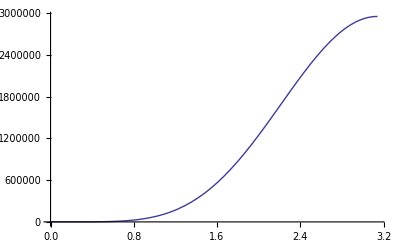

```mathematica
Plot[Sin[th/2]*(1+859*(1-Cos[th]))^2,{th,0,Pi}]
```

```mathematica
myversion2=1/r 2.517786554021126*^-12 BrfpG rfp^(-1+(4-nu)/2) rmono^(nu/2) Abs[Sin[thfp/2]] ((573.2018484873198 etaeletilde zetatilde (1-Cos[thfp]))/gammatilde)^2
```

1/(gammatilde^2 r)8.27245×10^-7 BrfpG etaeletilde^2 rfp^(-1+(4-nu)/2) rmono^(nu/2) zetatilde^2 Abs[Sin[thfp/2]] (1-Cos[thfp])^2

```mathematica
FullSimplify[(4-nu)/2-1]
```

1-nu/2

```mathematica
diff//.theconstsfull//.physicalconsts//.{etaele->0.1}
```

-4.21758×10^-13

```mathematica
Eicgevform=10^(-6)*Simplify[PowerExpand[gammaesyn^2*Epeakobskev//.{gamma0->mygamma0,omegaffp->myomegaffp}//.Tobsconsts2//.simpleconsts//.physicalconsts]]
```

(0.000747716 BrfpG omegaffp rfp^(2-nu/2) rmono^(nu/2) (8.1871×10^-7 gamma √(1-1/gamma0^2) gamma0+3.32108×10^-24 etaele omegaffp^2 rfp^2 zeta-3.32108×10^-24 etaele omegaffp^2 rfp^2 zeta Cos[thfp])^4 Sin[thfp/2])/(gamma^4 (-1.+gamma0^2)^2 r)

```mathematica
Eicgevform//.theconstsfull//.physicalconsts//.{etaele->0.05}
```

22.3742

```mathematica
573*2
```

1146

```mathematica
gammaeinj//.{etaele->0.1}
```

1/(√((c^4 gamma^2 (-1+gamma0^2) me^2)/((c^2 gamma √(1-1/gamma0^2) gamma0 me+0.2 mb omegaffp^2 rfp^2 zeta-0.2 mb omegaffp^2 rfp^2 zeta Cos[thfp])^2)))

```mathematica
(10^(-6))*Epeakobskevinj*gammaesyn^2//.Tobsconsts2//.theconstsfull//.physicalconsts
```

291483. (0.000325457+1.86552 etaele)^4

```mathematica
Tpeak=Epeak/kb//.theconstsfull//.physicalconsts
Tpeakobs=gamma*Tpeak//.theconstsfull//.physicalconsts
```

0.000058435 √bsqsyn gammaesyn^2

0.0409045 √bsqsyn gammaesyn^2

```mathematica
Epeakobskev*gammae^2//.theconstsfull//.physicalconsts
```

(5.03557×10^-12 √bsqsyn gammaesyn^2 gammajet)/(1-(2.52957×10^-10 (2+2.52957×10^-10 T) T)/((1+2.52957×10^-10 T)^2))

```mathematica
gammae//.solsT//.theconstsfull//.physicalconsts
```

1.12252

```mathematica
Pinj=(4/3)*sigmat*c*um*gammaesyn^2
Pinjform=Simplify[PowerExpand[Pinj//.Tobsconsts2//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]]
Pinjform//.theconstsfull//.physicalconsts//.{etaele->0.2}
```

(2 BrfpG^2 gammaesyn^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat Sin[thfp/2]^2)/(3 c gamma^2 π r^2)

1/(gamma^4 r^2)0.00122332 BrfpG^2 rfp^(2-nu) rmono^nu (4.64938×10^-7 gamma+0.000186552 etaele zeta-0.000186552 etaele zeta Cos[thfp])^2 Sin[thfp/2]^2

1198.68

```mathematica
tauinj=gammaesyn*me*c^2/Pinj//.{r->myr}
tauinjobs=tauinj/(2*gamma);
tauinjobsform=Simplify[PowerExpand[tauinjobs//.Tobsconsts2//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]]
tauinjobsform//.theconstsfull//.physicalconsts//.{etaele->0.2}
```

(5.94499 √c gamma (-1.+gamma0^2)^(1/4) √Lptilde me rfp^(1.-1. nu) rmono^(-2+1. nu) (rmono/rfp)^(2-nu) Csc[thfp/2]^2 Sin[0.5 thfp])/(gammaesyn mb omegaffp^(3/2) √sigmat √(npairs zeta))

(1.86948×10^-7 gamma √Lptilde rfp^(0.5+0. nu) rmono^(0. nu) Csc[thfp/2]^2 Sin[0.5 thfp])/(√npairs √zeta (4.64938×10^-7 gamma+0.000186552 etaele zeta-0.000186552 etaele zeta Cos[thfp]))

7.04936×10^-10

```mathematica
god=FullSimplify[tauinjobsform/Epeakobskevinjtest*gammaesyn^3]//.Tobsconsts2//.{r->myr};
godform=Simplify[PowerExpand[god//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts//.{ Sin[0.5 thfp]-> Sin[thfp/2]}],{thfp>0,Sin[thfp/2]>0}]
```

(2.57387×10^6 Lptilde^(3/4) rfp^(0.75+0. nu) rmono^(0. nu))/(√gamma npairs^(3/4) zeta^(3/4) Sin[thfp/2]^(3/2))

```mathematica
(1+0.00018655238653433792 etaele zeta/(4.6493815405179025*^-7 gamma)-0.00018655238653433792 etaele zeta Cos[thfp]/(4.6493815405179025*^-7 gamma))//.{gamma->gammatilde*700,zeta->zetatilde*10^4,etaele->etaeletilde*0.1}
```

1+(573.202 etaeletilde zetatilde)/gammatilde-(573.202 etaeletilde zetatilde Cos[thfp])/gammatilde

```mathematica
(* L = gamma^2 * gamma / gamma *)
Pj=2*Pi*Integrate[r^2*Sin[th]*mu*rhob*c^2*gamma*vp0,{th,0,thetajet}]
Pj//.theconsts//.physicalconsts
(* No longer can evaluate at fp since only have mono part of solution *)
Pj=2*Pi*Integrate[r^2*Sin[th]*mu*rhob*c^2*gamma*vp0,{th,0,thetajet}]
Pj//.{thetajet->Pi/2,BrfpG->10^(15),rfp->rl,rl->3*G*msun/c^2,zeta->10^4,gamma->gamma0,r->rfp,rp->r}

(* Check power at large radii -- seems reasonable *)
Pj=2*Pi*Integrate[r^2*th*mu*rhob*c^2*gamma*c,{th,0,thetajet}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
thepower=Pj//.theconsts//.physicalconsts
```

(2 BrfpG^2 c (-0.0345989+0.0345989 gamma0^2) π rfp^2 (rmono/rfp)^nu Sin[(rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)/gamma0

1.83607×10^51

(2 BrfpG^2 c (-0.0345989+0.0345989 gamma0^2) π rfp^2 (rmono/rfp)^nu Sin[(rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)/gamma0

1/(c^3 gamma0)2000000000000000000000000000000 3^(2-nu) G^2 (-0.0345989+0.0345989 gamma0^2) msun^2 π ((c^2 rmono)/(G msun))^nu Sin[3^(nu/2) ((c^2 rmono)/(G msun))^(-nu/2) Sin[thfp/2]]^2

0.217391 BrfpG^2 c √(1-1/gamma0^2) gamma0 rfp^2 Sin[thfp/2]^2

3.70107×10^9 BrfpG^2 rfp^2 Sin[thfp/2]^2

3.71825×10^51

```mathematica
dtco=886
dtlab=gamma*dtco//.theconstsfull//.physicalconsts
rlab=c*dtlab//.physicalconsts
```

886

620200

1.85931×10^16

```mathematica
(* thermal photosphere peak *)
```

```mathematica
Tobs0=FullSimplify[((T/.solsT)*gamma)]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Tobs=Tobs0//.theconsts//.physicalconsts
Tkev=1000*(1/ergPmev)*(kb*Tobs0)//.theconstsfull//.physicalconsts
```

(0.00120943 c^5 me^3 omegaffp^2)/(3.4641 kb Lptilde npairs omegaffp q^4+188.496 c gamma kb Lptilde^2 npairs^2 q^4 sigmat)

(1.24358×10^-12)/((2.76118×10^-65 gamma Lptilde^2 npairs^2+(1.90744×10^-43 Lptilde npairs)/rfp) rfp^2)

(6.3377×10^-24)/(4.30607×10^-49 npairs+1.93282×10^-62 npairs^2)

29217.4

```mathematica
theconstsfull
```

{BrfpG→3.2×10^15,lmode→1,mmode→1/10,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,Lptilde→1,1→1,r→50000000000000,npairs→(3 BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(8 c^2 gamma mb π r^2 zeta)}

```mathematica
(* note, not at rtrans here! So can't use normal parameters *)
sols=Solve[tauabs==1,T]
whichroot=2
mysol=sols[[whichroot,1,2]];
mysol//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.{npairs->0}//.theconstsfull//.physicalconsts
Tobsabs0=FullSimplify[((mysol)*gamma)]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Tabskev=1000*(1/ergPmev)*(kb*Tobsabs0)//.{npairs->ne*100}//.theconstsfull//.physicalconsts
```

{{T→-((4.62133+8.00437 ⅈ) BrfpG^(2/3) kb^(1/3) Lptilde^(1/3) npairs^(1/3) omegaffp^(1/3) q^(4/3) rfp^(4/3) (rmono/rfp)^(0.333333 nu) Sin[0.5 thfp]^(2/3))/(arad^(1/3) c^(7/3) gamma^(1/3) me r^(2/3))},{T→-((4.62133-8.00437 ⅈ) BrfpG^(2/3) kb^(1/3) Lptilde^(1/3) npairs^(1/3) omegaffp^(1/3) q^(4/3) rfp^(4/3) (rmono/rfp)^(0.333333 nu) Sin[0.5 thfp]^(2/3))/(arad^(1/3) c^(7/3) gamma^(1/3) me r^(2/3))},{T→(9.24265 BrfpG^(2/3) kb^(1/3) Lptilde^(1/3) npairs^(1/3) omegaffp^(1/3) q^(4/3) rfp^(4/3) (rmono/rfp)^(0.333333 nu) Sin[0.5 thfp]^(2/3))/(arad^(1/3) c^(7/3) gamma^(1/3) me r^(2/3))}}

2

0

-1/(arad^(1/3) c^(7/3) me r^(2/3))(4.62133-8.00437 ⅈ) BrfpG^(2/3) gamma^(2/3) kb^(1/3) Lptilde^(1/3) npairs^(1/3) omegaffp^(1/3) q^(4/3) rfp^(4/3) (rmono/rfp)^(0.333333 nu) Sin[0.5 thfp]^(2/3)

-1/r^(2/3)(3.52124×10^-7-6.09896×10^-7 ⅈ) BrfpG^(2/3) gamma^(2/3) Lptilde^(1/3) npairs^(1/3) rfp^(1-0.333333 nu) rmono^(0.333333 nu) Sin[0.5 thfp]^(2/3)

-15.513+26.8693 ⅈ

```mathematica
(* Get and look at T at tauabs==1 *)
```

```mathematica
(* //.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts//.theconstsfullnornopairs//.physicalconsts*)
solsr=Solve[tauabs==1,r]
tauabs1r=solsr[[2,1,2]]//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts
myTsols=Solve[pm==pg,T]//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts
godT=myTsols[[1,1,2]]//.{r->tauabs1r}
Theta=PowerExpand[godT]*kb/(me*c^2)//.{T->Th*me*c^2/kb}//.physicalconsts
myThtilde=FullSimplify[FullSimplify[Theta/0.1,{BrfpG>0,rfp>0,rmono>0,thfp>0,zeta>0}]//.{zeta->10^4*zetatilde,BrfpG->BrfpGtilde*(3.2*10^(15)),rfp->rfptilde*(3*msun*G/c^2),Th->Thtilde*0.1}//.physicalconsts]
test=Theta//.{zeta->myzeta}//.theconstsfullnornopairs//.physicalconsts
solsTh=Solve[test==Th,Th]
solsTh//.{myzeta->10^4}
godTh=solsTh[[3,1,2]]
LogLogPlot[godTh,{myzeta,1,10^4}]
(.000388*700*me*c^2)/ergPmev*10^3//.physicalconsts
```

```mathematica
solsgodT=Solve[godT==T,T]
solsgodT//.theconstsfullnornopairs//.physicalconsts
Tattauabs=PowerExpand[solsgodT[[3,1,2]]]
Tattauabs//.theconstsfullnornopairs//.physicalconsts
```

```mathematica
(* IGNORE REST OF BELOW *)
```

```mathematica
(* across single layer *)
taulocal=FullSimplify[ne*sigmat*di//.{rp->r},{ne0>0,r>0,BrfpG>0,rfp>0,zeta>0}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
taulocal//.theconsts//.physicalconsts
```

(BrfpG c mb rfp sigmat √((√(1-1/gamma0^2) gamma0 q^2 (rmono/rfp)^nu)/(c^2 gamma mb^2 zeta)))/(8 √2 π q^2 r)

(2.93593×10^-17 BrfpG rfp^(1-nu/2) rmono^(nu/2))/(√gamma r √zeta)

2.03835×10^-11

```mathematica
(* across entire jet in comoving frame *)
Rjet=r*thetajet
taulocal2=FullSimplify[ne*sigmat*Rjet//.{rp->r},{ne0>0,r>0,BrfpG>0,rfp>0,zeta>0}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
taulocal2//.theconsts//.physicalconsts
```

2 r (rmono/rfp)^(-nu/2) Sin[thfp/2]

(BrfpG^2 √(1-1/gamma0^2) gamma0 rfp^2 (rmono/rfp)^(nu/2) sigmat Sin[thfp/2])/(8 c^2 gamma mb π r zeta)

(1.00695×10^-23 BrfpG^2 rfp^(2-nu/2) rmono^(nu/2) Sin[thfp/2])/(gamma r zeta)

2.64848

```mathematica
(* across entire jet in lab frame *)
taulocal3=FullSimplify[ne*sigmat*gamma*r*2*thetajet//.{rp->r},{ne0>0,r>0,BrfpG>0,rfp>0,zeta>0}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
taulocal3//.theconsts//.physicalconsts
```

(BrfpG^2 √(1-1/gamma0^2) gamma0 rfp^2 (rmono/rfp)^(nu/2) sigmat Sin[thfp/2])/(4 c^2 mb π r zeta)

(2.01389×10^-23 BrfpG^2 rfp^(2-nu/2) rmono^(nu/2) Sin[thfp/2])/(r zeta)

3707.87

```mathematica
(*If[whichsetup==1,vr=0.1*va;,vr=eta/deltasp;];*)
(* assume fast reconnection *)
vr=0.1*va;
```

```mathematica
(* one layer dissipating *)
Lr=(2*bsq*vr)*(2*Lp)*(2*Pi*Rjet)//.{Lp->Rjet}
Lrobs=FullSimplify[Lr*gamma,{BrfpG>0,rfp>0,r>0,zeta>0}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Lrobs//.solsT1[[1]]//.theconsts//.physicalconsts
```

(1263.31 BrfpG^2 Lptilde omegaffp rfp^2 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2]^3)/(gamma r)

(1263.31 BrfpG^2 Lptilde omegaffp rfp^4 (rmono/rfp)^(nu/2) Sin[thfp/2]^3)/r

(9.46827×10^12 BrfpG^2 Lptilde rfp^(3-nu/2) rmono^(nu/2) Sin[thfp/2]^3)/r

Part::partd: Part specification solsT1 ⟦ 1 ⟧ is longer than depth of object.

ReplaceRepeated::reps: {solsT1 ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification solsT1 ⟦ 1 ⟧ is longer than depth of object.

ReplaceRepeated::reps: {solsT1 ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

3.86099×10^48//.solsT1⟦1⟧

```mathematica
(* multiple layers dissipating *)
Rjet=r*thetajet
Nc=f*Rjet/di
Lr=(2*bsq*vr)*(2*Lp)*(2*Pi*Rjet)*(Nc)//.{Lp->Rjet}
Lrobs=FullSimplify[Lr*gamma]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
result=Lrobs//.theconsts//.physicalconsts
```

2 r (rmono/rfp)^(-nu/2) Sin[thfp/2]

(√2 f r (rmono/rfp)^(-nu/2) √((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rmono^2 (rmono/rfp)^(-2+nu))/(c^2 gamma mb^2 r^2 zeta)) Sin[thfp/2])/c

1/(c gamma)1786.59 BrfpG^2 f Lptilde omegaffp rfp^4 √((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rmono^2 (rmono/rfp)^(-2+nu))/(c^2 gamma mb^2 r^2 zeta)) Sin[thfp/2]^4

(1786.59 BrfpG^2 f Lptilde omegaffp rfp^4 √((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rfp^2 (rmono/rfp)^nu)/(c^2 gamma mb^2 r^2 zeta)) Sin[thfp/2]^4)/c

(3.24736×10^6 BrfpG^3 f Lptilde rfp^(4-nu/2) rmono^(nu/2) Sin[thfp/2]^4)/(√gamma r √zeta)

5.01667×10^59 f

```mathematica
result//.{f->2*10^(-9)}
```

1.00333×10^51

```mathematica
Pj=2*Pi*Integrate[r^2*Sin[th]*mu*rhob*c^2*gamma*vp0,{th,0,Pi/2}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
EisoperDt=Pj//.theconsts//.physicalconsts
```

(2 BrfpG^2 c (-0.0172995+0.0172995 gamma0^2) π rfp^2 (rmono/rfp)^nu)/gamma0

9.13829×10^8 BrfpG^2 rfp^(2-nu) rmono^nu

7.70848×10^54

```mathematica
(* L = gamma^2 * gamma / gamma *)
Pj=2*Pi*Integrate[r^2*Sin[th]*mu*rhob*c^2*gamma*vp0,{th,0,thetajet}]
Pj//.theconsts//.physicalconsts
(* No longer can evaluate at fp since only have mono part of solution *)
Pj=2*Pi*Integrate[r^2*Sin[th]*mu*rhob*c^2*gamma*vp0,{th,0,thetajet}]
Pj//.{thetajet->Pi/2,BrfpG->10^(15),rfp->rl,rl->3*G*msun/c^2,zeta->10^4,gamma->gamma0,r->rfp,rp->r}

(* Check power at large radii -- seems reasonable *)
Pj=2*Pi*Integrate[r^2*th*mu*rhob*c^2*gamma*c,{th,0,thetajet}]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
thepower=Pj//.theconsts//.physicalconsts
```

(2 BrfpG^2 c (-0.0345989+0.0345989 gamma0^2) π rfp^2 (rmono/rfp)^nu Sin[(rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)/gamma0

1.83607×10^51

(2 BrfpG^2 c (-0.0345989+0.0345989 gamma0^2) π rfp^2 (rmono/rfp)^nu Sin[(rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)/gamma0

1/(c^3 gamma0)2000000000000000000000000000000 3^(2-nu) G^2 (-0.0345989+0.0345989 gamma0^2) msun^2 π ((c^2 rmono)/(G msun))^nu Sin[3^(nu/2) ((c^2 rmono)/(G msun))^(-nu/2) Sin[thfp/2]]^2

0.217391 BrfpG^2 c √(1-1/gamma0^2) gamma0 rfp^2 Sin[thfp/2]^2

3.70107×10^9 BrfpG^2 rfp^2 Sin[thfp/2]^2

3.71825×10^51

```mathematica
myf=Solve[result==thepower,f][[1]]
```

{f→7.41179×10^-9}

```mathematica
Num=FullSimplify[f*Rjet/di]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Num//.theconsts//.myf//.physicalconsts
Num//.{f->2*10^(-9)}//.theconsts//.physicalconsts
```

(√2 f r (rmono/rfp)^(-nu/2) √((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rfp^2 (rmono/rfp)^nu)/(c^2 gamma mb^2 r^2 zeta)) Sin[thfp/2])/c

(3.42973×10^-7 BrfpG f rfp Sin[thfp/2])/(√gamma √zeta)

963.031

259.864

```mathematica
v=0.999*c
gamma=1/Sqrt[1-(v/c)^2]
gamma^2
Clear[v,gamma]
```

0.999 c

22.3663

500.25

```mathematica
(* Check stuff *)
Integrate[2*Pi*Sin[th],{th,0,Pi}]
```

4 π

```mathematica
rhob//.{r->10^6,BrfpG->10^(15),rfp->r,zeta->10^4,gamma->1.15}
rhofp//.{r->10^6,BrfpG->10^(15),rfp->r,zeta->10^4}
(* gamma rho0 r^2 sin(th) = constant *)
rhob//.theconsts//.physicalconsts
```

(3.45989×10^12 1000000^(2-nu) √(1-1/gamma0^2) gamma0 rmono^nu)/c^2

12500000000000000000000000/(c^2 π)

1.21185×10^-11

```mathematica
Rjet=r*thetajet
dttransit=Lp/va//.{Lp->Rjet}
dtobs=dttransit/gamma
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
dtobs//.theconsts//.physicalconsts
```

2 r (rmono/rfp)^(-nu/2) Sin[thfp/2]

(62.8319 gamma Lptilde)/omegaffp

(62.8319 Lptilde)/omegaffp

8.38338×10^-9 Lptilde rfp

0.00371355

```mathematica
Tobs0=FullSimplify[((T/.solsT1)*gamma)]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Tobs=Tobs0//.theconsts//.physicalconsts
Tkev=1000*(1/ergPmev)*(kb*Tobs0)//.theconsts//.physicalconsts
```

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

gamma (T/.solsT1)

gamma (T/.solsT1)

700 (T/.solsT1)

0.0000603217 (T/.solsT1)

```mathematica
7667*(fcover/myfcover)^(1/4)//.theconsts//.physicalconsts//.{myfcover->2*10^(-9)/80.}
```

3.42879×10^6 fcover^(1/4)

```mathematica
(8*Pi/3)*lambdac^2
```

(10 q^4)/(27 kb^2 T^2)

```mathematica
X=dttransit*nucg//.{Lp->Rjet}/.solsT1
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
X//.theconsts//.physicalconsts
X//.footconsts//.physicalconsts
```

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(c^8 me^4 r^2)33073.4 BrfpG^2 kb Lptilde^2 npairs q^4 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) sigmat (2 √3+(188.496 c gamma Lptilde npairs sigmat)/omegaffp) T Sin[thfp/2]^2/.solsT1

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

1/r^2 3.59691×10^-49 BrfpG^2 Lptilde^2 npairs rfp^(4-nu) (2 √3+5.01456×10^-22 gamma Lptilde npairs rfp) rmono^nu T Sin[thfp/2]^2/.solsT1

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

1.19071×10^-19 (2 √3+1.5549×10^-13 npairs) npairs T/.solsT1

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

0.00151706 Lptilde^2 npairs (2 √3+2.55448×10^-16 Lptilde npairs) T/.solsT1

```mathematica
theconsts
```

{BrfpG→3.2×10^15,lmode→1,mmode→1/10,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15,Lptilde→1,1→1,r→50000000000000}

```mathematica
X//.{fcover->1/500000000,thetajet->0.02,BrfpG->1000000000000000,rfp->rl,rl->(3 G msun)/c^2,zeta->10000,gamma->700,r->10^(18),rp->r,nu->3/4,rmono->30000000000,thfp->π/2,omegaffp->(0.25 c)/rfp,gamma0->1.15}//.physicalconsts
```

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

2.907×10^-29 Lptilde^2 npairs (2 √3+1.5549×10^-13 Lptilde npairs) T/.solsT1

```mathematica
nuc
```

(25 c npairs q^4 √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(2 √6 kb^2 T^2 (1+(3 kb T)/(2 c^2 me)))

```mathematica
Xs=dttransit*nuc//.{Lp->Rjet}/.solsT1
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
Xs//.theconsts//.physicalconsts
Xs//.footconsts//.physicalconsts
```

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(320.637 c gamma Lptilde npairs q^4 √((kb T (2+(3 kb T)/(2 c^2 me)))/(c^2 me)))/(kb^2 omegaffp T^2 (1+(3 kb T)/(2 c^2 me)))/.solsT1

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

(4.64937×10^-8 gamma Lptilde npairs rfp √(2+2.52957×10^-10 T))/((1+2.52957×10^-10 T) T^(3/2))/.solsT1

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

(14.4166 npairs √((2+2.52957×10^-10 T) T))/((1+2.52957×10^-10 T) T^2)/.solsT1

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

(0.0236844 Lptilde npairs √((2+2.52957×10^-10 T) T))/((1+2.52957×10^-10 T) T^2)/.solsT1

```mathematica
Xs//.{fcover->1/500000000,thetajet->0.02,BrfpG->1000000000000000,rfp->rl,rl->(3 G msun)/c^2,zeta->10000,gamma->700,r->10^(18),rp->r,nu->3/4,rmono->30000000000,thfp->π/2,omegaffp->(0.25 c)/rfp,gamma0->1.15}//.physicalconsts
```

ReplaceAll::reps: {solsT1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

(14.4166 Lptilde npairs √((2+2.52957×10^-10 T) T))/((1+2.52957×10^-10 T) T^2)/.solsT1